```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/pjoot/project/figures/blogit

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

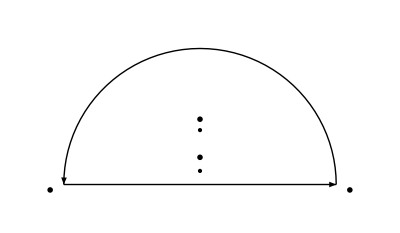

```mathematica
ClearAll[R, lineArrow, xrange1, r, semicircleArrow, greensDropWithResistanceFig1, epsilon]
R=5; 
r = 2;
epsilon = 0.5;
xrange1 = {{-R,0},{R, 0}};

lineArrow=Graphics[{
Thick,Arrow[xrange1],
Text[MaTeX["-R"], {-1.1 R, -0.2}],
Text[MaTeX["R"], {1.1 R, -0.2}],
Text[MaTeX["i \\gamma/m"], {0, 1.2 r}],
Text[MaTeX["i \\epsilon"], {0, 2 epsilon}],
PointSize -> Large,

Point[{0,r}],
Point[{0,epsilon}]
}];

semicircleArrow[a_, s_]:=Graphics[{Thick,Arrow[Table[{a Cos[t],a Sin[t]},{t,s,s + Pi,Pi/50}]]}]

greensDropWithResistanceFig1 = Show[lineArrow,semicircleArrow[R, 0],AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-1,R+1}},Axes->False,Ticks->None,Frame->False]
```

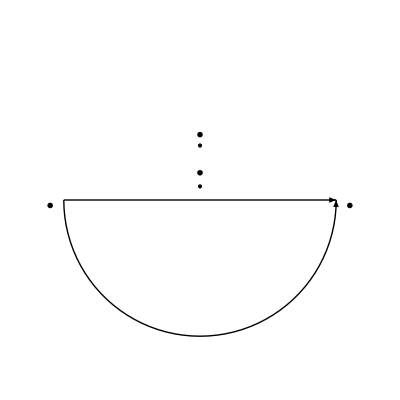

```mathematica
ClearAll[greensDropWithResistanceFig2]

greensDropWithResistanceFig2 = Show[lineArrow,semicircleArrow[R, Pi],AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-R-1,R+1}},Axes->False,Ticks->None,Frame->False]
```

```mathematica
peeters`exportForLatex["greensDropWithResistanceFig1",greensDropWithResistanceFig1]
peeters`exportForLatex["greensDropWithResistanceFig2",greensDropWithResistanceFig2]
```

{greensDropWithResistanceFig1.eps,greensDropWithResistanceFig1pn.png}

{greensDropWithResistanceFig2.eps,greensDropWithResistanceFig2pn.png}